```mathematica
$Version

projectDir=FileNameJoin[{$HomeDirectory,"Documents","physics-informed-financial-ml"}]

Quiet[CreateDirectory[FileNameJoin[{projectDir,#}],CreateIntermediateDirectories->True]]&/@{"data/raw","data/processed","mathematica","python","results/figures","results/tables","results/models","docs"};

CopyFile[FileNameJoin[{$HomeDirectory,"Downloads","SP500_2011_2026.csv"}],FileNameJoin[{projectDir,"data","raw","SP500_2011_2026.csv"}]]

FileNames["*",FileNameJoin[{projectDir,"data","raw"}]]
```

13.0.1 for Microsoft Windows (64-bit) (January 28, 2022)

C:\Users\Rishi Vyas\Documents\physics-informed-financial-ml

C:\Users\Rishi Vyas\Documents\physics-informed-financial-ml\data\raw\SP500_2011_2026.csv

{C:\Users\Rishi Vyas\Documents\physics-informed-financial-ml\data\raw\SP500_2011_2026.csv}

```mathematica
projectDir=FileNameJoin[{$HomeDirectory,"Documents","physics-informed-financial-ml"}];
rawFile=FileNameJoin[{projectDir,"data","raw","SP500_2011_2026.csv"}];

raw=Import[rawFile,"CSV"];

Dimensions[raw]
raw[[1]]
raw[[2;;4]]//TableForm
raw[[-3;;]]//TableForm
Head/@raw[[2]]
```

{3773,7}

{Date,Open,High,Low,Close,Adj Close,Volume}

2011-04-01 | 1329.48 | 1337.85 | 1328.89 | 1332.41 | 1332.41 | 4223740000
2011-04-04 | 1333.56 | 1336.74 | 1329.1 | 1332.87 | 1332.87 | 4223740000
2011-04-05 | 1332.03 | 1338.21 | 1330.03 | 1332.63 | 1332.63 | 3852280000

2026-03-30 | 6403.37 | 6427.31 | 6316.91 | 6343.72 | 6343.72 | 5458640000
2026-03-31 | 6395.88 | 6539.05 | 6395.88 | 6528.52 | 6528.52 | 6396100000
2026-04-01 | 6556.56 | 6609.67 | 6554.29 | 6575.32 | 6575.32 | 5637260000

{String,Real,Real,Real,Real,Real,Integer}

```mathematica
header=First[raw];
data=Rest[raw];

dates=DateObject[{#,{"Year","-","Month","-","Day"}},"Day"]&/@data[[All,1]];
values=data[[All,2;;7]];
gaps=Differences[AbsoluteTime/@dates]/86400;

Dataset[<|"Trading days"->Length[data],"First date"->First[dates],"Last date"->Last[dates],"Strictly increasing dates"->AllTrue[gaps,Positive],"Duplicate dates"->Length[dates]-Length[DeleteDuplicates[dates]],"Non-numeric values"->Count[values,x_/;!NumericQ[x],{2}],"Prices <= 0"->Count[values[[All,1;;5]],x_/;x<=0,{2}],"Zero-volume days"->Count[values[[All,6]],0],"OHLC violations"->Count[values,{o_,h_,l_,c_,_,_}/;!(l<=Min[o,c]&&h>=Max[o,c])],"Close != Adj Close"->Count[values,{_,_,_,c_,a_,_}/;c!=a],"Calendar gaps {days, count}"->Sort[Tally[gaps]]|>]
```

```mathematica
Sort[Tally[gaps]]

zeroPos=Flatten[Position[values[[All,6]],0]]
data[[zeroPos[[1]]-2;;zeroPos[[1]]+2]]//TableForm

Select[Transpose[{Most[dates],Rest[dates],gaps}],#[[3]]>=5&]//TableForm
```

{{1,2948},{2,40},{3,682},{4,100},{5,1}}

{3057}

2023-05-22 | 4190.78 | 4209.22 | 4179.68 | 4192.63 | 4192.63 | 3728520000
2023-05-23 | 4176.8 | 4185.68 | 4142.54 | 4145.58 | 4145.58 | 4155320000
2023-05-24 | 4132.96 | 4132.96 | 4103.98 | 4115.24 | 4115.24 | 0
2023-05-25 | 4155.71 | 4165.74 | 4129.73 | 4151.28 | 4151.28 | 4147760000
2023-05-26 | 4156.16 | 4212.87 | 4156.16 | 4205.45 | 4205.45 | 3715460000

Fri 26 Oct 2012 | Wed 31 Oct 2012 | 5

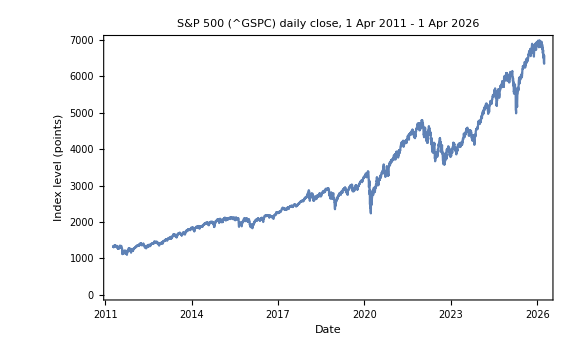

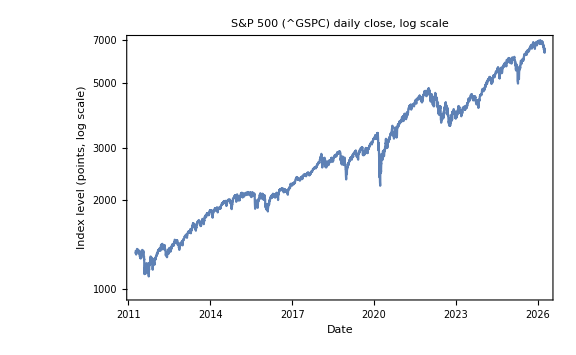

```mathematica
close=TimeSeries[Transpose[{dates,values[[All,4]]}]];

pClose=DateListPlot[close,PlotLabel->"S&P 500 (^GSPC) daily close, 1 Apr 2011 - 1 Apr 2026",FrameLabel->{"Date","Index level (points)"},ImageSize->Large]

pCloseLog=DateListLogPlot[close,PlotLabel->"S&P 500 (^GSPC) daily close, log scale",FrameLabel->{"Date","Index level (points, log scale)"},ImageSize->Large]

Export[FileNameJoin[{projectDir,"results","figures","01_close_linear.png"}],pClose];
Export[FileNameJoin[{projectDir,"results","figures","01_close_log.png"}],pCloseLog];
```

3771

{Mon 4 Apr 2011,0.000345179,0.000345179}

{1.59633,1.59633}

{0.000423318,0.010927}

{Mon 16 Mar 2020,-0.127652}

{Wed 9 Apr 2025,0.0908949}

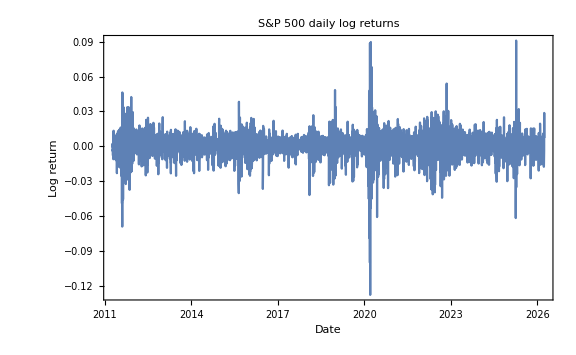

```mathematica
logP=Log[close["Values"]];
r=Differences[logP];
rDates=Rest[dates];
returns=TimeSeries[Transpose[{rDates,r}]];

Length[r]
{First[rDates],First[r],Log[1332.87/1332.41]}

{Total[r],Log[Last[close["Values"]]/First[close["Values"]]]}

{Mean[r],StandardDeviation[r]}
{rDates[[First@Ordering[r,1]]],Min[r]}
{rDates[[First@Ordering[r,-1]]],Max[r]}

pRet=DateListPlot[returns,PlotRange->All,PlotLabel->"S&P 500 daily log returns",FrameLabel->{"Date","Log return"},ImageSize->Large]
Export[FileNameJoin[{projectDir,"results","figures","02_log_returns.png"}],pRet];
```

{-0.633527,17.3807}

{28,0.238865}

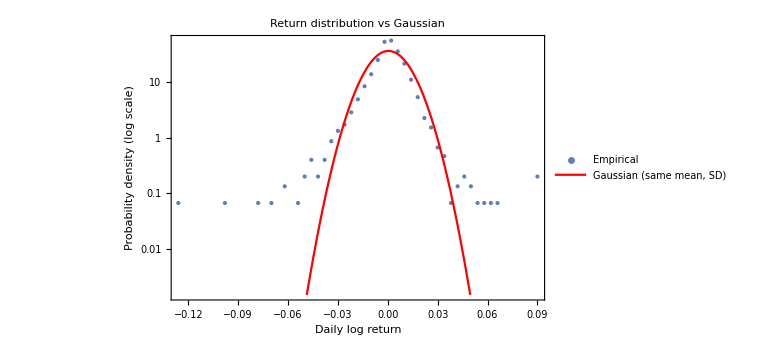

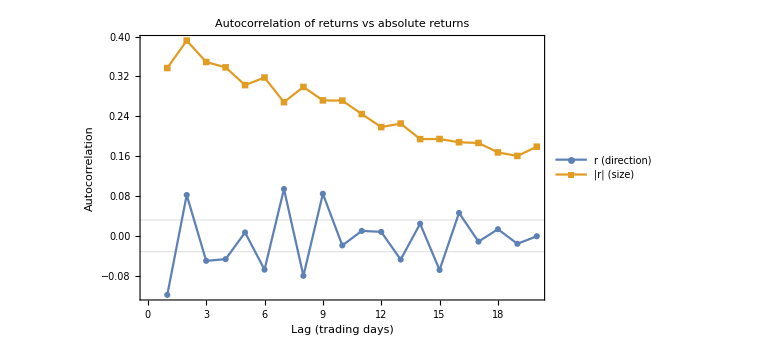

```mathematica
mu=Mean[r];sd=StandardDeviation[r];

{Skewness[r],Kurtosis[r]}

z=(r-mu)/sd;
{Count[z,x_/;Abs[x]>4],N[Length[r]*2*(1-CDF[NormalDistribution[],4])]}

{bins,dens}=HistogramList[r,{-0.14,0.10,0.004},"PDF"];
pts=Select[Transpose[{MovingAverage[bins,2],dens}],#[[2]]>0&];
pDist=Show[ListLogPlot[pts,PlotStyle->PointSize[Medium],PlotLegends->{"Empirical"}],LogPlot[PDF[NormalDistribution[mu,sd],x],{x,mu-4.5 sd,mu+4.5 sd},PlotStyle->Red,PlotLegends->{"Gaussian (same mean, SD)"}],PlotRange->All,Frame->True,ImageSize->Large,FrameLabel->{"Daily log return","Probability density (log scale)"},PlotLabel->"Return distribution vs Gaussian"]

band=1.96/Sqrt[Length[r]];
pACF=ListPlot[{Rest[CorrelationFunction[r,{20}]],Rest[CorrelationFunction[Abs[r],{20}]]},DataRange->{1,20},Joined->True,PlotMarkers->Automatic,PlotLegends->{"r (direction)","|r| (size)"},GridLines->{None,{-band,band}},Frame->True,ImageSize->Large,FrameLabel->{"Lag (trading days)","Autocorrelation"},PlotLabel->"Autocorrelation of returns vs absolute returns"]

Export[FileNameJoin[{projectDir,"results","figures","03_return_distribution.png"}],pDist];
Export[FileNameJoin[{projectDir,"results","figures","04_acf_returns_vs_abs.png"}],pACF];
```

3767

{Fri 8 Apr 2011,{Mon 4 Apr 2011,Tue 5 Apr 2011,Wed 6 Apr 2011,Thu 7 Apr 2011,Fri 8 Apr 2011}}

{0.00482945,0.00482945}

{0.0109322,0.010927}

{0.00136219,0.0162352,0.200982}

Wed 18 Mar 2020

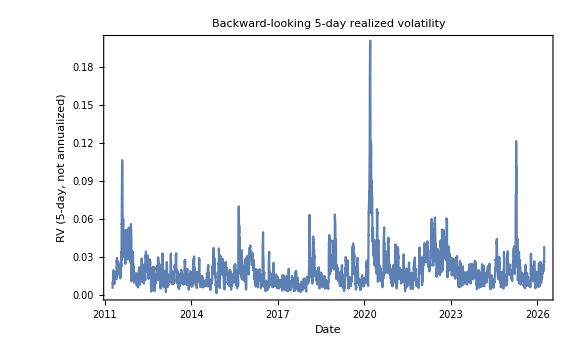

```mathematica
rv5=Table[Sqrt[Total[r[[t-4;;t]]^2]],{t,5,Length[r]}];
rv5Dates=rDates[[5;;]];

Length[rv5]
{rv5Dates[[1]],rDates[[1;;5]]}
{rv5[[1]],Sqrt[Total[r[[1;;5]]^2]]}

{Sqrt[Mean[rv5^2]/5],sd}

{Min[rv5],Median[rv5],Max[rv5]}
rv5Dates[[First@Ordering[rv5,-1]]]

pRV5=DateListPlot[TimeSeries[Transpose[{rv5Dates,rv5}]],PlotRange->All,PlotLabel->"Backward-looking 5-day realized volatility",FrameLabel->{"Date","RV (5-day, not annualized)"},ImageSize->Large]
Export[FileNameJoin[{projectDir,"results","figures","05_rv5_backward.png"}],pRV5];
```

3766

{Mon 4 Apr 2011,{Tue 5 Apr 2011,Wed 6 Apr 2011,Thu 7 Apr 2011,Fri 8 Apr 2011,Mon 11 Apr 2011}}

{Wed 25 Mar 2026,{Thu 26 Mar 2026,Fri 27 Mar 2026,Mon 30 Mar 2026,Tue 31 Mar 2026,Wed 1 Apr 2026}}

True

0.

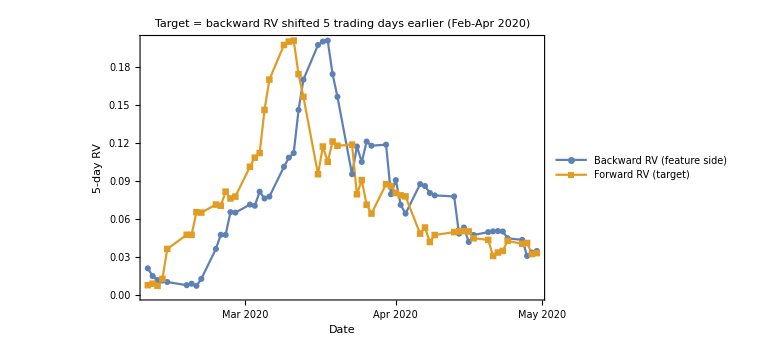

```mathematica
nR=Length[r];
rvFwd=Table[Sqrt[Total[r[[t+1;;t+5]]^2]],{t,1,nR-5}];
rvFwdDates=rDates[[1;;nR-5]];

Length[rvFwd]
{rvFwdDates[[1]],rDates[[2;;6]]}
{Last[rvFwdDates],rDates[[nR-4;;nR]]}

rvFwd==Rest[rv5]
Max[Abs[rvFwd-Rest[rv5]]]

win={DateObject[{2020,2,10}],DateObject[{2020,4,30}]};
pShift=DateListPlot[{TimeSeriesWindow[TimeSeries[Transpose[{rv5Dates,rv5}]],win],TimeSeriesWindow[TimeSeries[Transpose[{rvFwdDates,rvFwd}]],win]},PlotLegends->{"Backward RV (feature side)","Forward RV (target)"},PlotMarkers->Automatic,Joined->True,ImageSize->Large,FrameLabel->{"Date","5-day RV"},PlotLabel->"Target = backward RV shifted 5 trading days earlier (Feb-Apr 2020)"]
Export[FileNameJoin[{projectDir,"results","figures","06_target_vs_backward_rv.png"}],pShift];
```

```mathematica
idx=Range[5,nR-5];
cols={"Date","Close","LogReturn","RV5_past","RV5_target"};
ds=Table[{rDates[[t]],values[[t+1,4]],r[[t]],rv5[[t-4]],rvFwd[[t]]},{t,idx}];

Length[ds]
TableForm[ds[[{1,2,-2,-1}]],TableHeadings->{None,cols}]

Count[ds[[All,2;;5]],x_/;!NumericQ[x],{2}]
ds[[1;;-6,5]]==ds[[6;;,4]]

Correlation[ds[[All,4]],ds[[All,5]]]

outFile=FileNameJoin[{projectDir,"data","processed","sp500_rv5_dataset.csv"}];
Export[outFile,Prepend[{DateString[#[[1]],"ISODate"],#[[2]],#[[3]],#[[4]],#[[5]]}&/@ds,cols]];

chk=Import[outFile,"CSV"];
Dimensions[chk]
Max[Abs[Flatten[chk[[2;;,3;;5]]-ds[[All,3;;5]]]]]
```

3762

Date | Close | LogReturn | RV5_past | RV5_target
Fri 8 Apr 2011 | 1328.17 | -0.00401251 | 0.00482945 | 0.00917429
Mon 11 Apr 2011 | 1324.46 | -0.00279723 | 0.00557036 | 0.0141098
Tue 24 Mar 2026 | 6556.37 | -0.00374961 | 0.0239108 | 0.0382373
Wed 25 Mar 2026 | 6591.9 | 0.00540453 | 0.0203277 | 0.0385215

0

True

0.666033

{3763,5}

0.